## Power-law

```mathematica
f0=10^-2.6527;
α10=7.40138;
α20=2.0219;
ms0=8.11295;
i0=30;
j0=10;
```

## mass function

```mathematica
Pbp[m_,ms_,α1_,α2_]:=1/ms(1/(α1+1)+1/(α2-1))^-1*Piecewise[{{(m/ms)^α1,m<ms},{(m/ms)^-α2,m>=ms}}]
Integrate[Pbp[i,ms,α1,α2],{i,0,∞},Assumptions->{α1>0,α2>1,ms>0}]
```

1

```mathematica
Integrate[Pbp[i,ms,α1,α2],{i,10^-1,10^3},Assumptions->{α1>0,α2>1,ms>1,ms<30}]/.{α1->α10,α2->α20,ms->ms0}
```

0.994947

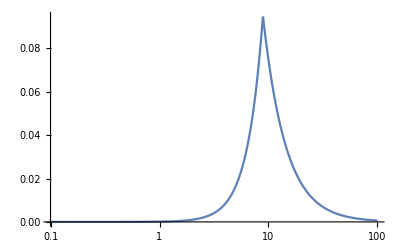

```mathematica
LogLinearPlot[Pbp[m,ms0,α10,α20], {m,10^-1,100},PlotRange->All]
```

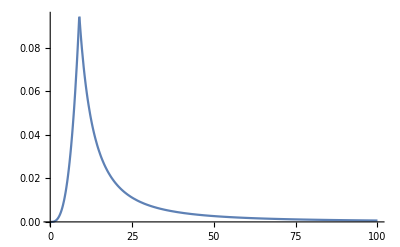

```mathematica
Plot[Pbp[m,ms0,α10,α20], {m,10^-1,100},PlotRange->All]
```

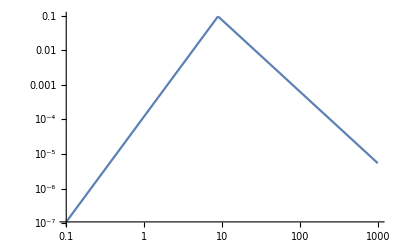

```mathematica
LogLogPlot[Pbp[m,ms0,α10,α20], {m,10^-1,1000},PlotRange->All]
```

## m_pbh

```mathematica
1/Integrate[Pbp[i,ms,α1,α2]/i,{i,0,∞},Assumptions->{α1>0,α2>1,ms>0}]
mpbh[ms_,α1_,α2_]:=(ms α1 α2)/((1+α1) (-1+α2))
```

(ms α1 α2)/((1+α1) (-1+α2))

## F(m)

```mathematica
F[i_,ms_,α1_,α2_]:=Pbp[i,ms,α1,α2]*mpbh[ms,α1,α2]/i;
F[i,ms,α1,α2]//FullSimplify
```

(α1 α2 (Piecewise[{{(i/ms)^α1, i<ms}, {(i/ms)^-α2, True}}]))/(i α1+i α2)

```mathematica
Integrate[F[i,ms,α1,α2],{i,0,∞},Assumptions->{α1>0,α2>1,ms>0}]
```

1

## R1

```mathematica
Integrate[l^(-21/37)F[l,ms,α1,α2],{l,0,∞},Assumptions->{α1>21/37,α2>1,ms>0}]
```

(1369 α1 α2)/(ms^(21/37) (-21+37 α1) (21+37 α2))

```mathematica
Integrate[l^(-21/37)F[l,ms,α1,α2],{l,10^-1,10^3},Assumptions->{α1>0,α2>1,ms>1, ms<30}]//Simplify
```

(37 α1 α2 (-(10^(58/37-α1) ms^-α1)/(α1+α2)+370/(ms^(21/37) (21+37 α2))+(10^(-26/37-3 α2) ms^α2 (21-37 α1))/((α1+α2) (21+37 α2))))/(10 (-21+37 α1))

```mathematica
1.32*10^6*(f/mpbh[ms,α1,α2])^(53/37)(37 α1 α2 (-(10^(58/37-α1) ms^-α1)/(α1+α2)+370/(ms^(21/37) (21+37 α2))+(10^(-26/37-3 α2) ms^α2 (21-37 α1))/((α1+α2) (21+37 α2))))/(10 (-21+37 α1))*(i*j)^(3/37)*(i+j)^(36/37)F[i,ms,α1,α2]*F[j,ms,α1,α2]//Simplify
```

```mathematica
mergerRateDensity1st[f_,i_,j_,ms_,α1_,α2_]:=-(3.583229926788547*^7 10^(-α1-3 α2) f (i+j)^(36/37) ms^(-58/37-α1) α1^2 (1.+α1) (-1.+α2) ((f (1+α1) (-1+α2))/(ms α1 α2))^(16/37) α2^2 (10^α1 ms^(21/37+α1+α2) (-0.5675675675675675+1. α1)+10^(α1+3 α2) ms^α1 (-50.4315948717136 α1-50.4315948717136 α2)+1000^α2 ms^(21/37) (105.7518177042237+186.32463119315602 α2)) (Piecewise[{{(i/ms)^α1, i<ms}, {(i/ms)^-α2, i≥ms}, {0, True}}]) (Piecewise[{{(j/ms)^α1, j<ms}, {(j/ms)^-α2, j≥ms}, {0, True}}]))/((i j)^(34/37) (-21.+37. α1) (α1+α2)^3 (21.+37. α2))

mergerRateDensity1st[f0,i0,j0,ms0,α10,α20]
```

0.0266871

```mathematica
{f0,i0,j0,ms0,α10,α20}
```

{0.00239883,30,10,8.89,3.05,2.07}

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[f_,i_,j_,ms_,α1_,α2_]:=(1.32*^6 f (i+j)^(36/37) α1^2 (1.+α1) (-1.+α2) ((f (1+α1) (-1+α2))/(ms α1 α2))^(16/37) α2^2 (Piecewise[{{(i/ms)^α1, i<ms}, {(i/ms)^-α2, i≥ms}, {0, True}}]) (Piecewise[{{(j/ms)^α1, j<ms}, {(j/ms)^-α2, j≥ms}, {0, True}}]))/((i j)^(34/37) ms^(58/37) (-0.5675675675675675+1. α1) (α1+α2)^2 (0.5675675675675675+1. α2));
```

```mathematica
mergerRateDensity1st[f,i,j,ms,α1,α2]
```

0.00430068

## R2

```mathematica
Integrate[l^(-42/37)*F[l,ms,α1,α2],{l,0,∞},Assumptions->{α1>42/37,α2>1,ms>0}]
```

(1369 α1 α2)/(ms^(42/37) (-42+37 α1) (42+37 α2))

```mathematica
Integrate[l^(-42/37)*F[l,ms,α1,α2],{l,10^-1,10^3},Assumptions->{α1>0,α2>1,ms>1, ms<30}]//Simplify
```

(37 α1 α2 (10^(-126/37-3 α2) ms^(42/37+α2) (-42+37 α1)-37 (α1+α2)+10^(42/37-α1) ms^(42/37-α1) (42+37 α2)))/(ms^(42/37) (42-37 α1) (α1+α2) (42+37 α2))

```mathematica
mergerRateDensity2nd0[f_,i_,j_,k_,ms_,α1_,α2_]:=1.59*10^4*(f/mpbh[ms,α1,α2])^(69/37)k^(6/37)(37 α1 α2 (10^(-126/37-3 α2) ms^(42/37+α2) (-42+37 α1)-37 (α1+α2)+10^(42/37-α1) ms^(42/37-α1) (42+37 α2)))/(ms^(42/37) (42-37 α1) (α1+α2) (42+37 α2))(i+j)^(6/37)(i+j+k)^(72/37)F[i,ms,α1,α2]*F[j,ms,α1,α2]*F[k,ms,α1,α2]
```

```mathematica
mergerRateDensity2nd0[f,i-e,e,j,ms,α1,α2]//Simplify
```

```mathematica
{f0,i0,2,j0,ms0,α10,α20}
```

{0.00239883,30,2,10,8.89,3.05,2.07}

```mathematica
mergerRateDensity2nd000[f0,i0,2,j0,ms0,α10,α20]
```

1.27956×10^-6

```mathematica
mergerRateDensity2nd000[f_,i_,e_,j_,ms_,α1_,α2_]:=-((8558.450970832304 10^(-α1-3 α2) f i^(6/37) (i+j)^(72/37) ms^(-79/37-α1) α1^3 (1.+α1) (-1.+α2) ((f (1+α1) (-1+α2))/(ms α1 α2))^(32/37) α2^3 (10^α1 ms^(42/37+α1+α2) (-1.135135135135135+1. α1)+10^(α1+3 α2) ms^α1 (-2543.34576130465 α1-2543.34576130465 α2)+1000^α2 ms^(42/37) (39408.336863490695+34716.86818926562 α2)) (Piecewise[{{(e/ms)^α1, e<ms}, {(e/ms)^-α2, e≥ms}, {0, True}}]) (Piecewise[{{((-e+i)/ms)^α1, i<e+ms}, {((-e+i)/ms)^-α2, i≥e+ms}, {0, True}}]) (Piecewise[{{(j/ms)^α1, j<ms}, {(j/ms)^-α2, j≥ms}, {0, True}}]))/(e (-1. e+i) j^(31/37) (-42.+37. α1) (α1+α2)^4 (42.+37. α2)))
```

```mathematica
mergerRateDensity2nd0[f_,i_,j_,e_,ms_,α1_,α2_]:=(2.17671*^7 i^(6/37) (i+j)^(72/37) α1^4 ((f (1+α1) (-1+α2))/(ms α1 α2))^(69/37) α2^4 (Piecewise[{{(e/ms)^α1, e<ms}, {(e/ms)^-α2, e≥ms}, {0, True}}]) (Piecewise[{{((-e+i)/ms)^α1, -e+i<ms}, {((-e+i)/ms)^-α2, -e+i≥ms}, {0, True}}]) (Piecewise[{{(j/ms)^α1, j<ms}, {(j/ms)^-α2, j≥ms}, {0, True}}]))/(e (-e+i) j^(31/37) ms^(42/37) (1+α1)^3 (-42+37 α1) (1/(1+α1)+1/(-1+α2))^3 (-1+α2)^3 (42+37 α2))
```

```mathematica
mergerRateDensity2nd1[f_,i_,j_,ms_,α1_,α2_]:=(2.17671*^7 i^(6/37) (i+j)^(72/37) α1^4 ((f (1+α1) (-1+α2))/(ms α1 α2))^(69/37) α2^4  (Piecewise[{{(j/ms)^α1, j<ms}, {(j/ms)^-α2, j≥ms}, {0, True}}]))/( j^(31/37) ms^(42/37) (1+α1)^3 (-42+37 α1) (1/(1+α1)+1/(-1+α2))^3 (-1+α2)^3 (42+37 α2))NIntegrate[(Piecewise[{{(e/ms)^α1, e<ms}, {(e/ms)^-α2, e≥ms}, {0, True}}]) (Piecewise[{{((-e+i)/ms)^α1, -e+i<ms}, {((-e+i)/ms)^-α2, -e+i≥ms}, {0, True}}])/(e (-e+i)),{e,10^-1,i},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

```mathematica
mergerRateDensity2nd[f_,i_,j_,ms_,α1_,α2_]:=1/2(mergerRateDensity2nd1[f,i,j,ms,α1,α2]+mergerRateDensity2nd1[f,j,i,ms,α1,α2])
```

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,ms_?NumericQ,α1_?NumericQ,α2_?NumericQ]:=mergerRateDensity2nd[f,i,j,ms,α1,α2]/mergerRateDensity1st[f,i,j,ms,α1,α2];
```

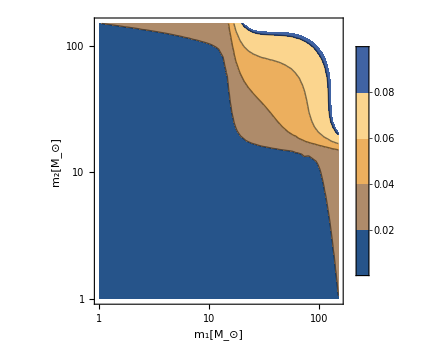

```mathematica
mMin=1;
mMax=150;

ContourPlot[ratioR[f0,i,j,ms0,α10,α20],{i,mMin,mMax},{j,mMin,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-log.pdf",%]*)
```